```mathematica
makeChain[n_] := Table[0, {i, n}]
makeEmptyIndexes[n_] :=  Table[i, {i,1, n}]
getChainIndexes[chain_] := Table[i, {i, Length[chain]}]
createNeighbours[node_] := {node - 1, node + 1}
inBoundaries[node_, N_] := node >= 1 && node ≤ N
```

```mathematica
findIsolatedClusters[chain_, startNode_, chainSize_] := {isolatedClusterCount = 0; isolatedCount = 0;
howLong = Length[chain];
startNodes =Join[{startNode}, Select[createNeighbours[startNode], # ≥ 1 && # ≤ chainSize &]]; 
visited={};
 toVisit = {};centers = {};
While[Length[startNodes] > 0 ,firstNode = Extract[startNodes,1]; startNodes = startNodes[[2;;]];
toVisit = Append[toVisit, firstNode];
currentType = chain[[firstNode]];
currentCount = 0; (* used to count how many members are in cluster if it's a cluster *)
fine = False;
While[Length[toVisit] > 0, node = Extract[toVisit, 1]; toVisit = toVisit[[2;;]];
nodeType = chain[[node]];
If[nodeType == 0,fine = True;, If[nodeType == currentType,
currentCount ++;visited = Append[visited, node]; startNodes = DeleteCases[startNodes, node]; neighbourNodes = createNeighbours[node];
neighbour1 = neighbourNodes[[1]];
neighbour2 = neighbourNodes[[2]];
If[inBoundaries[neighbour1, howLong], If[!MemberQ[visited, neighbour1], 
toVisit = Append[toVisit, neighbour1];], fine=True];
If[inBoundaries[neighbour2, howLong], If[!MemberQ[visited, neighbour2], toVisit = Append[toVisit, neighbour2];], fine=True];];];
];If[!fine, (* we found an isolated cluster *) isolatedClusterCount++; centers = Append[centers, firstNode]; isolatedCount = isolatedCount + currentCount;]];
{isolatedClusterCount, centers, isolatedCount}}
```

```mathematica
simulateChain[maxLength_, types_:2] := Module[{maxLen = maxLength, isolatedCountArray, notIsolatedCountArray, emptyIndexes, chain, iter}, iter = 0;
allIsolated = 0;
isolatedCountArray = {};
notIsolatedCountArray = {};
emptyIndexes = makeEmptyIndexes[maxLen];
chain = makeChain[maxLen];
While[Length[emptyIndexes] > 0, 
iter++;
(* fill the random empty place with random type *)
x = RandomChoice[emptyIndexes]; emptyIndexes = DeleteCases[emptyIndexes, x]; 
chain[[x]] = RandomChoice[Table[i, {i, 1, types}]]; 

clusters = findIsolatedClusters[chain, x, maxLength];
isolated = clusters[[1, 3]];

allIsolated += isolated;
isolatedCountArray = Append[isolatedCountArray, allIsolated];
notIsolatedCountArray = Append[notIsolatedCountArray, iter - allIsolated];];
{notIsolatedCountArray, isolatedCountArray}]
```

```mathematica
Timing[maxLen = 1000;
countsArrayAll ={};
countsArray = simulateChain[maxLen];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
```

{0.15343,Null}

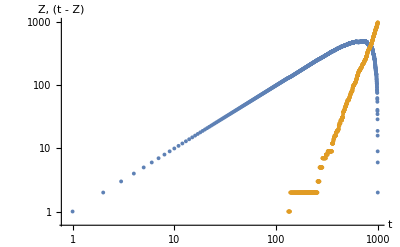

```mathematica
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

```mathematica
maxLen = 1000;

For[i=0,i<20,i++,countsArray = simulateChain[maxLen, 2];Z = countsArray[[2]];
Clear[x];
qp = ListPlot[Z];
fit = Fit[Z, { 1 ,x, x^2,  x^3}, x ];
]
```

$Aborted

General::ivar: 3239 is not a valid variable.

Fit[{{100,1117/40},{600,943/10},{1100,6003/40},{1600,7817/40},{2100,4783/20},{2600,12267/40},{3100,5647/20}},{3239^(2/3)},3239]

General::ivar: 3239. is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

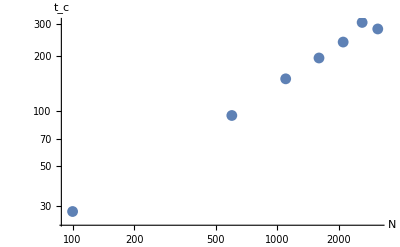

```mathematica
allTCs = {};
allMeanTCs = {};
maxLens = {};
For[g= 100, g < 4000,g+= 500,
For[i=0,i<40,i++,countsArray = simulateChain[g, 2];Z = countsArray[[2]];
Clear[x];
tC = Length@First@Split[Z,#1==0&];
allTCs = Append[allTCs, tC];
];
maxLens = Append[maxLens, g];
allMeanTCs = Append[allMeanTCs, Mean[allTCs]];
allTCs = {};
];
data = Transpose[{maxLens,allMeanTCs}];
fit = Fit[data, { x ^ (2 / 3)}, x];
Print[fit];
Show[ListLogLogPlot[data], LogLogPlot[fit, {x,1, 4000}], AxesLabel -> {"N", "t_c"}]
```

{{131/4,1939/40,663/10,3421/40},{128/5,807/20,511/10,309/5},{943/40,1379/40,227/5,1119/20}}

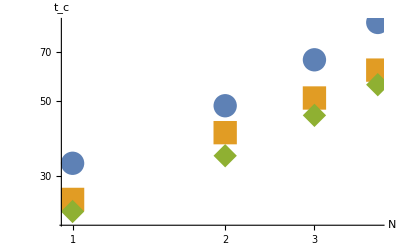

1.37659 x^(2/3)

```mathematica
allTCs = {};
allMeanTCs = {};
allMeanTCsPerM = {};
maxLens = {};
For[m=2, m < 16, m *= 2,
For[g= 100, g < 500,g+= 100,
For[i=0,i<40,i++,
countsArray = simulateChain[g, m];Z = countsArray[[2]];
	Clear[x];
tC = Length@First@Split[Z,#1==0&];
allTCs = Append[allTCs, tC];
];
maxLens = Append[maxLens, g];
allMeanTCs = Append[allMeanTCs, Mean[allTCs]];
allTCs = {};
];
data = Transpose[{maxLens,allMeanTCs}];allMeanTCsPerM = Append[allMeanTCsPerM, allMeanTCs];allMeanTCs = {};
maxLens = {};
];

Print[allMeanTCsPerM ];ListLogLogPlot[allMeanTCsPerM, AxesLabel -> {"N", "t_c"}, PlotMarkers->{Automatic,24} ]
```

```mathematica
getZAndRest[maxLen_, types_:2] := Module[{allZ, allRest, i},
allZ = {};
allRest = {};
For[i=0,i<10,i++,countsArray = simulateChain[maxLen, types];Z = countsArray[[2]];
allZ = Append[allZ, Z];
allRest = Append[allRest, countsArray[[1]]];
];
meanZ = Mean[allZ];
meanRest = Mean[allRest];
{meanZ, meanRest} ]
```

```mathematica
{meanZ100, meanRest100} = getZAndRest[100];
{meanZ200, meanRest200} = getZAndRest[200];
{meanZ400, meanRest400} = getZAndRest[400];
{meanZ800, meanRest800} = getZAndRest[800];
```

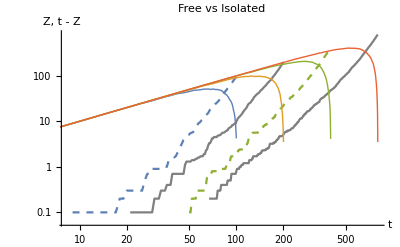

```mathematica
Show[ListLogLogPlot[{meanZ100, meanZ200, meanZ400, meanZ800}, PlotStyle->{Dashed, Gray}, Joined->True], ListLogLogPlot[{meanRest100, meanRest200, meanRest400, meanRest800}, PlotStyle->Thick, Joined->True] , AxesLabel->{HoldForm[t],HoldForm["Z, t - Z"]},PlotLabel->HoldForm[Free vs Isolated]]
```

### Bring me more dimensions! Or at least two for now! ;)

```mathematica
createNeighboursLattice[node_] := {{node[[1]] - 1, node[[2]]}, {node[[1]] + 1, node[[2]]}, {node[[1]], node[[2]] - 1}, {node[[1]], node[[2]] + 1}}
```

```mathematica
inBoundariesLattice[node_, howLong_] := node[[1]] ≥ 1 && node[[2]] ≥ 1 && node[[1]] ≤ howLong && node[[2]] ≤ howLong
```

```mathematica
findIsolatedClustersOnLattice[chain_, startNode_, chainSize_] := {isolatedClusterCount = 0; isolatedCount = 0;
howLong = Length[chain];
startNodes =Join[{startNode}, Select[createNeighboursLattice[startNode], inBoundariesLattice[#, chainSize] &]]; 
visited={};
 toVisit = {};centers = {};
While[Length[startNodes] > 0 ,firstNode = Extract[startNodes,1]; startNodes = startNodes[[2;;]];
toVisit = Append[toVisit, firstNode];
currentType = Extract[chain, firstNode];
currentCount = 0; (* used to count how many members are in cluster if it's a cluster *)
fine = False;
While[Length[toVisit] > 0, node = Extract[toVisit, 1]; toVisit = toVisit[[2;;]];
nodeType = Extract[chain,  node];
If[nodeType == 0,fine = True;, If[nodeType == currentType,
currentCount ++;visited = Append[visited, node]; startNodes = DeleteCases[startNodes, node];
neighbourNodes = createNeighboursLattice[node];
neighbour1 = neighbourNodes[[1]];
neighbour2 = neighbourNodes[[2]];
neighbour3 = neighbourNodes[[3]];
neighbour4 = neighbourNodes[[4]];
If[inBoundariesLattice[neighbour1, howLong], If[!MemberQ[visited, neighbour1], 
toVisit = Append[toVisit, neighbour1];], fine=True];
If[inBoundariesLattice[neighbour3, howLong], If[!MemberQ[visited, neighbour3], 
toVisit = Append[toVisit, neighbour3];], fine=True];
If[inBoundariesLattice[neighbour4, howLong], If[!MemberQ[visited, neighbour4], 
toVisit = Append[toVisit, neighbour4];], fine=True];
If[inBoundariesLattice[neighbour2, howLong], If[!MemberQ[visited, neighbour2], toVisit = Append[toVisit, neighbour2];], fine=True];];];
];If[!fine, (* we found an isolated cluster *) isolatedClusterCount++; centers = Append[centers, firstNode]; isolatedCount = isolatedCount + currentCount;]];
{isolatedClusterCount, centers, isolatedCount}}
```

```mathematica
chain = {{1, 1, 1}, {1, -1, 1}, {1, 1, 1}}
```

{{1,1,1},{1,-1,1},{1,1,1}}

```mathematica
findIsolatedClustersOnLattice[chain, {2, 2}, 3]
```

{{1,{{2,2}},1}}

```mathematica
lattice = {{1, 1, 1, 1, 1}, {1, 1, 0, -1, 1}, {1, -1, 1, 1, 1}, {1, 1, -1, 1, 1}, {1, 1, 1, 1, 1}}
```

{{1,1,1,1,1},{1,1,0,-1,1},{1,-1,1,1,1},{1,1,-1,1,1},{1,1,1,1,1}}

```mathematica
lattice // TableForm
```

1 | 1 | 1 | 1 | 1
1 | 1 | 0 | -1 | 1
1 | -1 | 1 | 1 | 1
1 | 1 | -1 | 1 | 1
1 | 1 | 1 | 1 | 1

```mathematica
findIsolatedClustersOnLattice[lattice, {3,3}, 4]
```

{{2,{{4,3},{3,2}},2}}

```mathematica
makeLattice[n_] := Table[Table[0, {i, n}], {j, n}]
```

```mathematica
makeEmptyIndexesLattice[maxLen_] := Tuples[Table[i, {i, 1, maxLen}],2]
```

```mathematica
simulateLattice[maxLength_, types_:2] := Module[{maxLen = maxLength, isolatedCountArray, notIsolatedCountArray, emptyIndexes, chain, iter}, iter = 0;
allIsolated = 0;
isolatedCountArray = {};
notIsolatedCountArray = {};
emptyIndexes = makeEmptyIndexesLattice[maxLen];
chain = makeLattice[maxLen];
While[Length[emptyIndexes] > 0, 
iter++;
(* fill the random empty place with random type *)
x = RandomChoice[emptyIndexes]; emptyIndexes = DeleteCases[emptyIndexes, x]; 
chain[[x[[1]], x[[2]]]] = RandomChoice[Table[i, {i, 1, types}]]; 

clusters = findIsolatedClustersOnLattice[chain, x, maxLength];
isolated = clusters[[1, 3]];
allIsolated += isolated;
isolatedCountArray = Append[isolatedCountArray, allIsolated];
notIsolatedCountArray = Append[notIsolatedCountArray, iter - allIsolated];];
{notIsolatedCountArray, isolatedCountArray}]
```

```mathematica
simulateLattice[5]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,24},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Timing[maxLen = 20;
countsArrayAll ={};
countsArray = simulateLattice[maxLen];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
```

{2.22254,Null}

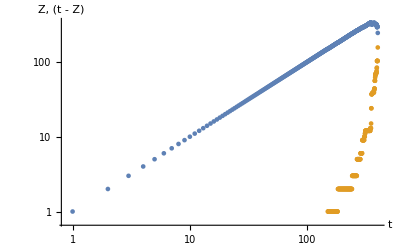

```mathematica
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

```mathematica
empiricalDistribution=EmpiricalDistribution[{2/3,1/3}->{1,2}]
```

DataDistribution[…]

```mathematica
RandomVariate[empiricalDistribution]
```

1

```mathematica
simulateChainWithBias[maxLength_, bias_] := Module[{maxLen = maxLength, isolatedCountArray, notIsolatedCountArray, emptyIndexes, chain, iter}, iter = 0;
allIsolated = 0;
isolatedCountArray = {};
notIsolatedCountArray = {};
emptyIndexes = makeEmptyIndexes[maxLen];
chain = makeChain[maxLen];
While[Length[emptyIndexes] > 0, 
iter++;
(* fill the random empty place with random type *)
x = RandomChoice[emptyIndexes]; emptyIndexes = DeleteCases[emptyIndexes, x]; 
empiricalDistribution=EmpiricalDistribution[{1 /2 + bias,1/ 2 - bias}->{1,2}];
chain[[x]] = RandomVariate[empiricalDistribution]; 

clusters = findIsolatedClusters[chain, x, maxLength];
isolated = clusters[[1, 3]];

allIsolated += isolated;
isolatedCountArray = Append[isolatedCountArray, allIsolated];
notIsolatedCountArray = Append[notIsolatedCountArray, iter - allIsolated];];
{notIsolatedCountArray, isolatedCountArray}]
```

{1.22684,Null}

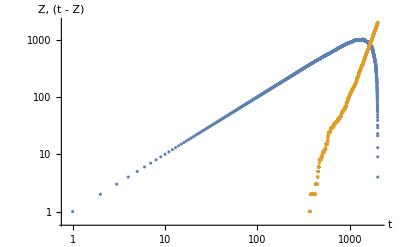

```mathematica
Timing[maxLen = 2000;
countsArrayAll ={};
countsArray = simulateChainWithBias[maxLen, 0.1];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

{1.25216,Null}

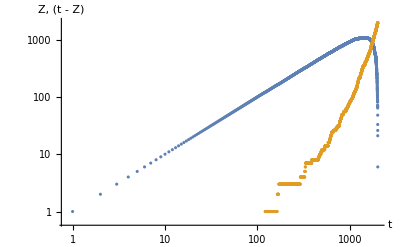

```mathematica
Timing[maxLen = 2000;
countsArrayAll ={};
countsArray = simulateChainWithBias[maxLen, 0.2];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

{1.27999,Null}

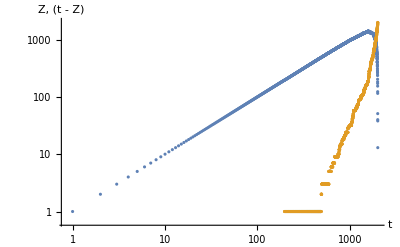

```mathematica
Timing[maxLen = 2000;
countsArrayAll ={};
countsArray = simulateChainWithBias[maxLen, 0.4];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

{1.49357,Null}

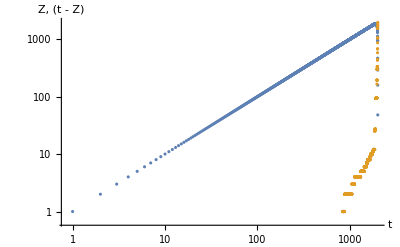

```mathematica
Timing[maxLen = 2000;
countsArrayAll ={};
countsArray = simulateChainWithBias[maxLen, 0.49];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

```mathematica
simulateLatticeWithBias[maxLength_, bias_] := Module[{maxLen = maxLength, isolatedCountArray, notIsolatedCountArray, emptyIndexes, chain, iter}, iter = 0;
allIsolated = 0;
isolatedCountArray = {};
notIsolatedCountArray = {};
emptyIndexes = makeEmptyIndexesLattice[maxLen];
chain = makeLattice[maxLen];
While[Length[emptyIndexes] > 0, 
iter++;
(* fill the random empty place with random type *)
x = RandomChoice[emptyIndexes]; 

empiricalDistribution=EmpiricalDistribution[{1 /2 + bias,1/ 2 - bias}->{1,2}];
emptyIndexes = DeleteCases[emptyIndexes, x]; 
newVal = RandomVariate[empiricalDistribution]; 
chain[[x[[1]], x[[2]]]] = newVal;

clusters = findIsolatedClustersOnLattice[chain, x, maxLength];
isolated = clusters[[1, 3]];
allIsolated += isolated;
isolatedCountArray = Append[isolatedCountArray, allIsolated];
notIsolatedCountArray = Append[notIsolatedCountArray, iter - allIsolated];];
{notIsolatedCountArray, isolatedCountArray}]
```

{6.62609,Null}

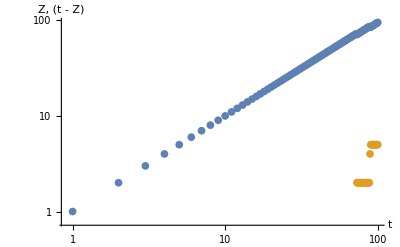

```mathematica
Timing[maxLen = 10;
countsArrayAll ={};
countsArray = simulateLatticeWithBias[maxLen, 0.4];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```